## Adaptive Step Bisection test!

### Setup

```mathematica
l=0; 
range={11.5,13.};
```

```mathematica
MakeGrid[{Δρ1_,Δρ2_,ρ0_,ρinf_}]:=Module[{i,grid,lo,hi},
grid={};
i=0;(*here i is playing the role of ρ*)
While[i<ρinf,
lo=.5Δρ2 Tanh[(i-ρ0)/100]+.5Δρ2+Δρ1;(*Subscript[ρ, n]-Subscript[ρ, n-1]*)
i=i+.5Δρ2 Tanh[(i-ρ0)/100]+.5Δρ2+Δρ1;(*ρ, updated*)
hi=.5Δρ2 Tanh[(i-ρ0)/100]+.5Δρ2+Δρ1;(*Subscript[ρ, n+1]-Subscript[ρ, n]*)
grid=Append[grid,{lo,i,hi}];
];
Return[grid]
]
```

```mathematica
Critical[λ_,consts_]:=Module[{H,res,ρs,nn,a,b,rho},
ρs=MakeGrid[consts];
nn=Length[ρs];
a[n_]:=ρs[[n,1]];
b[n_]:=ρs[[n,3]];
rho[n_]:=ρs[[n,2]];
H=SparseArray[{{n_,n_}:>4./(a[n]^2+b[n]^2)-2./rho[n] ⅇ^(-rho[n]/λ)+(l*(l+1))/(rho[n])^2,{n_, m_}/; Abs[n-m] == 1 :> -2./(a[n]^2+b[n]^2)},{nn,nn}, 0.];
H=N[H];
res=Sort[Eigenvalues[H,-25]];(*Went from 100 down to 25 eigenvalues, which sped this calculation up immensely with no apparent loss of information*)
Return[res]
]
```

```mathematica
CountNegs[list_]:=Module[{neg,i},
neg=0;
For[i=1,list[[i]]<0,i++,
neg++;
];
Return[neg]
]
```

```mathematica
Bisect[F_,consts_,x0_,val_,xf_,ϵ_]:=Module[{mid,newval,lnegs,vam,mnegs,vah},
mid=x0+Abs[x0-xf]/2;
Print["Bisecting. Midpoint is "<>ToString[mid]]; (*Again, lets you know it's working/progress*)
lnegs=CountNegs[val];
vam=F[mid,consts];
mnegs=CountNegs[vam];
If[xf-x0>ϵ,
If[lnegs<mnegs || (lnegs==mnegs && val[[1]] < vam[[1]]), (*if there is a zero on the lower half*)
Return[Bisect[F,consts,x0,val,mid,ϵ]];, (*bisect it*)
Return[Bisect[F,consts,mid,vam,xf,ϵ]]; (*otherwise try the upper half*)
];,
vah = F[xf,consts];
Return[{mid,lnegs,CountNegs[vah]}];
]
]
```

```mathematica
Findlc[F_,consts_,x0_,xf_,ϵ_]:=Module[{val,vah,lnegs,hnegs,res},
Print["****beginning calculation"];
val=F[x0,consts];
res=Bisect[F,consts,x0,val,xf,ϵ];
Return[res]
]
```

```mathematica
DistributeDefinitions[range,Bisect,Critical,MakeGrid,l,CountNegs,Findlc]
```

{range,Bisect,CountNegs,Critical,MakeGrid,l,Findlc}

## Collecting data. Defaults: {0.1, 2, 100, 25000}

### Varying ρ0

```mathematica
ρ0s=Table[i,{i,50,500,50}]
```

{50,100,150,200,250,300,350,400,450,500}

```mathematica
DistributeDefinitions[ρ0s];
```

```mathematica
varyr0=ParallelTable[Timing[Findlc[Critical,{0.1,2,ρ0s[[i]],25000},range[[1]],range[[2]],10^(-6)]],{i,1,10}]
```

****beginning calculation

****beginning calculation

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.4375

Bisecting. Midpoint is 12.4375

Bisecting. Midpoint is 12.5313

Bisecting. Midpoint is 12.5313

Bisecting. Midpoint is 12.4844

Bisecting. Midpoint is 12.4844

Bisecting. Midpoint is 12.4609

Bisecting. Midpoint is 12.4609

Bisecting. Midpoint is 12.4727

Bisecting. Midpoint is 12.4492

Bisecting. Midpoint is 12.4785

Bisecting. Midpoint is 12.4551

Bisecting. Midpoint is 12.4756

Bisecting. Midpoint is 12.4521

Bisecting. Midpoint is 12.4741

Bisecting. Midpoint is 12.4507

Bisecting. Midpoint is 12.4734

Bisecting. Midpoint is 12.45

Bisecting. Midpoint is 12.4738

Bisecting. Midpoint is 12.4496

Bisecting. Midpoint is 12.4739

Bisecting. Midpoint is 12.4494

Bisecting. Midpoint is 12.474

Bisecting. Midpoint is 12.4493

Bisecting. Midpoint is 12.4741

Bisecting. Midpoint is 12.4494

Bisecting. Midpoint is 12.4741

Bisecting. Midpoint is 12.4741

Bisecting. Midpoint is 12.4493

Bisecting. Midpoint is 12.4741

Bisecting. Midpoint is 12.4493

Bisecting. Midpoint is 12.4741

Bisecting. Midpoint is 12.4493

Bisecting. Midpoint is 12.4741

Bisecting. Midpoint is 12.4493

Bisecting. Midpoint is 12.4741

Bisecting. Midpoint is 12.4493

Bisecting. Midpoint is 12.4741

Bisecting. Midpoint is 12.4493

Bisecting. Midpoint is 12.4493

****beginning calculation

Bisecting. Midpoint is 12.25

****beginning calculation

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.4375

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.3438

Bisecting. Midpoint is 12.2969

Bisecting. Midpoint is 12.4375

Bisecting. Midpoint is 12.3203

Bisecting. Midpoint is 12.5313

Bisecting. Midpoint is 12.332

Bisecting. Midpoint is 12.5781

Bisecting. Midpoint is 12.3262

Bisecting. Midpoint is 12.6016

Bisecting. Midpoint is 12.3232

Bisecting. Midpoint is 12.5898

Bisecting. Midpoint is 12.3247

Bisecting. Midpoint is 12.584

Bisecting. Midpoint is 12.324

Bisecting. Midpoint is 12.5811

Bisecting. Midpoint is 12.3243

Bisecting. Midpoint is 12.5825

Bisecting. Midpoint is 12.3245

Bisecting. Midpoint is 12.5833

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.5836

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.5834

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.5833

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.5833

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.5833

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.5833

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.5833

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.5833

Bisecting. Midpoint is 12.5833

****beginning calculation

Bisecting. Midpoint is 12.5833

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.5833

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.4375

Bisecting. Midpoint is 12.3438

****beginning calculation

Bisecting. Midpoint is 12.2969

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.3203

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.332

Bisecting. Midpoint is 12.8125

Bisecting. Midpoint is 12.3379

Bisecting. Midpoint is 12.7188

Bisecting. Midpoint is 12.335

Bisecting. Midpoint is 12.6719

Bisecting. Midpoint is 12.3335

Bisecting. Midpoint is 12.6484

Bisecting. Midpoint is 12.3328

Bisecting. Midpoint is 12.6602

Bisecting. Midpoint is 12.3331

Bisecting. Midpoint is 12.666

Bisecting. Midpoint is 12.3329

Bisecting. Midpoint is 12.333

Bisecting. Midpoint is 12.6689

Bisecting. Midpoint is 12.333

Bisecting. Midpoint is 12.6704

Bisecting. Midpoint is 12.333

Bisecting. Midpoint is 12.6697

Bisecting. Midpoint is 12.333

Bisecting. Midpoint is 12.67

Bisecting. Midpoint is 12.333

Bisecting. Midpoint is 12.6699

Bisecting. Midpoint is 12.333

Bisecting. Midpoint is 12.67

Bisecting. Midpoint is 12.333

Bisecting. Midpoint is 12.67

Bisecting. Midpoint is 12.333

Bisecting. Midpoint is 12.67

Bisecting. Midpoint is 12.333

Bisecting. Midpoint is 12.67

****beginning calculation

Bisecting. Midpoint is 12.67

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.67

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.67

Bisecting. Midpoint is 12.8125

Bisecting. Midpoint is 12.67

Bisecting. Midpoint is 12.67

Bisecting. Midpoint is 12.7188

Bisecting. Midpoint is 12.6719

****beginning calculation

Bisecting. Midpoint is 12.6953

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.707

Bisecting. Midpoint is 12.7129

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.71

Bisecting. Midpoint is 12.8125

Bisecting. Midpoint is 12.7114

Bisecting. Midpoint is 12.7188

Bisecting. Midpoint is 12.7107

Bisecting. Midpoint is 12.7656

Bisecting. Midpoint is 12.7103

Bisecting. Midpoint is 12.7422

Bisecting. Midpoint is 12.7101

Bisecting. Midpoint is 12.7305

Bisecting. Midpoint is 12.7102

Bisecting. Midpoint is 12.7363

Bisecting. Midpoint is 12.7102

Bisecting. Midpoint is 12.7334

Bisecting. Midpoint is 12.7102

Bisecting. Midpoint is 12.7319

Bisecting. Midpoint is 12.7102

Bisecting. Midpoint is 12.7312

Bisecting. Midpoint is 12.7102

Bisecting. Midpoint is 12.7102

Bisecting. Midpoint is 12.7308

Bisecting. Midpoint is 12.7102

Bisecting. Midpoint is 12.7307

Bisecting. Midpoint is 12.7102

Bisecting. Midpoint is 12.7306

Bisecting. Midpoint is 12.7102

Bisecting. Midpoint is 12.7306

Bisecting. Midpoint is 12.7306

****beginning calculation

Bisecting. Midpoint is 12.7306

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.7306

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.7306

Bisecting. Midpoint is 12.8125

Bisecting. Midpoint is 12.7306

Bisecting. Midpoint is 12.7188

Bisecting. Midpoint is 12.7306

Bisecting. Midpoint is 12.7656

Bisecting. Midpoint is 12.7306

Bisecting. Midpoint is 12.7422

Bisecting. Midpoint is 12.7305

****beginning calculation

Bisecting. Midpoint is 12.7246

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.7275

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.7261

Bisecting. Midpoint is 12.7253

Bisecting. Midpoint is 12.8125

Bisecting. Midpoint is 12.7257

Bisecting. Midpoint is 12.7188

Bisecting. Midpoint is 12.7255

Bisecting. Midpoint is 12.7656

Bisecting. Midpoint is 12.7256

Bisecting. Midpoint is 12.7422

Bisecting. Midpoint is 12.7256

Bisecting. Midpoint is 12.7305

Bisecting. Midpoint is 12.7256

Bisecting. Midpoint is 12.7363

Bisecting. Midpoint is 12.7256

Bisecting. Midpoint is 12.7334

Bisecting. Midpoint is 12.7256

Bisecting. Midpoint is 12.7319

Bisecting. Midpoint is 12.7256

Bisecting. Midpoint is 12.7312

Bisecting. Midpoint is 12.7256

Bisecting. Midpoint is 12.7316

Bisecting. Midpoint is 12.7256

Bisecting. Midpoint is 12.7314

Bisecting. Midpoint is 12.7256

Bisecting. Midpoint is 12.7315

Bisecting. Midpoint is 12.7315

Bisecting. Midpoint is 12.7315

«6 more identical outputs»

```mathematica
arraysizesr0=Table[Length[MakeGrid[{0.1,2,ρ0s[[i]],25000}]],{i,1,10}];
```

```mathematica
timingr0=Table[{arraysizesr0[[i]],varyr0[[i,1]]},{i,1,Length[arraysizesr0]}]
```

```mathematica
timingr0={{11964,50.575},{12050,50.248000000000005},{12226,51.699},{12517,54.07},{12901,56.332},{13338,57.798},{13799,63.227000000000004},{14270,63.710999999999984},{14744,67.595},{15219,66.14500000000001}}
```

{{11964,50.575},{12050,50.248},{12226,51.699},{12517,54.07},{12901,56.332},{13338,57.798},{13799,63.227},{14270,63.711},{14744,67.595},{15219,66.145}}

```mathematica
r0vals=Table[{ρ0s[[i]],varyr0[[i,2,1]]},{i,1,Length[ρ0s]}]
```

```mathematica
r0vals={{50,12.47411859035492},{100,12.324426293373108},{150,12.333002924919128},{200,12.449331402778625},{250,12.583317399024963},{300,12.669992804527283},{350,12.710203051567078},{400,12.725611805915833},{450,12.730566382408142},{500,12.73152768611908}}
```

{{50,12.4741},{100,12.3244},{150,12.333},{200,12.4493},{250,12.5833},{300,12.67},{350,12.7102},{400,12.7256},{450,12.7306},{500,12.7315}}

### Varying Δρ1

```mathematica
drhos=Table[0.1*2^-i,{i,0,3}]
```

{0.1,0.05,0.025,0.0125}

```mathematica
DistributeDefinitions[drhos];
```

```mathematica
varydrho=ParallelTable[Timing[Findlc[Critical,{drhos[[i]],2,100,25000},range[[1]],range[[2]],10^(-6)]],{i,1,4}]
```

****beginning calculation

****beginning calculation

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.4375

Bisecting. Midpoint is 12.4375

Bisecting. Midpoint is 12.3438

Bisecting. Midpoint is 12.3438

Bisecting. Midpoint is 12.2969

Bisecting. Midpoint is 12.2969

Bisecting. Midpoint is 12.3203

Bisecting. Midpoint is 12.2734

Bisecting. Midpoint is 12.332

Bisecting. Midpoint is 12.2617

Bisecting. Midpoint is 12.3262

Bisecting. Midpoint is 12.2559

Bisecting. Midpoint is 12.3232

Bisecting. Midpoint is 12.2529

Bisecting. Midpoint is 12.3247

Bisecting. Midpoint is 12.2515

Bisecting. Midpoint is 12.324

Bisecting. Midpoint is 12.2522

Bisecting. Midpoint is 12.3243

Bisecting. Midpoint is 12.2526

Bisecting. Midpoint is 12.3245

Bisecting. Midpoint is 12.2524

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.2523

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.2523

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.2523

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.2523

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.2523

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.2523

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.2523

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.2523

Bisecting. Midpoint is 12.2523

****beginning calculation

Bisecting. Midpoint is 12.25

****beginning calculation

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.4375

Bisecting. Midpoint is 11.875

Bisecting. Midpoint is 12.3438

Bisecting. Midpoint is 12.0625

Bisecting. Midpoint is 12.2969

Bisecting. Midpoint is 12.1563

Bisecting. Midpoint is 12.2734

Bisecting. Midpoint is 12.2031

Bisecting. Midpoint is 12.2852

Bisecting. Midpoint is 12.2266

Bisecting. Midpoint is 12.2793

Bisecting. Midpoint is 12.2383

Bisecting. Midpoint is 12.2764

Bisecting. Midpoint is 12.2441

Bisecting. Midpoint is 12.2778

Bisecting. Midpoint is 12.2412

Bisecting. Midpoint is 12.2786

Bisecting. Midpoint is 12.2397

Bisecting. Midpoint is 12.2782

Bisecting. Midpoint is 12.239

Bisecting. Midpoint is 12.278

Bisecting. Midpoint is 12.2386

Bisecting. Midpoint is 12.2779

Bisecting. Midpoint is 12.2388

Bisecting. Midpoint is 12.278

Bisecting. Midpoint is 12.2387

Bisecting. Midpoint is 12.278

Bisecting. Midpoint is 12.2387

Bisecting. Midpoint is 12.278

Bisecting. Midpoint is 12.2387

Bisecting. Midpoint is 12.278

Bisecting. Midpoint is 12.2387

Bisecting. Midpoint is 12.278

Bisecting. Midpoint is 12.2387

Bisecting. Midpoint is 12.278

Bisecting. Midpoint is 12.2387

Bisecting. Midpoint is 12.278

Bisecting. Midpoint is 12.2387

Bisecting. Midpoint is 12.278

Bisecting. Midpoint is 12.2387

Bisecting. Midpoint is 12.2387

```mathematica
arraysizesdrho=Table[Length[MakeGrid[{drhos[[i]],2,100,25000}]],{i,1,4}];
```

```mathematica
timingdrho=Table[{arraysizesdrho[[i]],varydrho[[i,1]]},{i,1,4}]
```

```mathematica
timingdrho={{12050,50.997000000000014},{12358,51.978999999999985},{12520,54.257000000000005},{12602,52.52600000000001}}
```

{{12050,50.997},{12358,51.979},{12520,54.257},{12602,52.526}}

```mathematica
drhovals=Table[{drhos[[i]],varydrho[[i,2,1]]},{i,1,4}]
```

```mathematica
drhovals={{0.1,12.324426293373108},{0.05,12.277984738349915},{0.025,12.252294898033142},{0.0125,12.23869001865387}}
```

{{0.1,12.3244},{0.05,12.278},{0.025,12.2523},{0.0125,12.2387}}

### Varying Δρ2

```mathematica
drhos2=Table[2^i,{i,5,0,-1}]
```

{32,16,8,4,2,1}

```mathematica
DistributeDefinitions[drhos2];
```

```mathematica
varydrho2=ParallelTable[Timing[Findlc[Critical,{0.1,drhos2[[i]],100,25000},range[[1]],range[[2]],10^(-6)]],{i,1,6}]
```

****beginning calculation

****beginning calculation

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.8125

Bisecting. Midpoint is 12.9063

Bisecting. Midpoint is 12.9531

Bisecting. Midpoint is 12.9766

Bisecting. Midpoint is 12.9883

Bisecting. Midpoint is 12.9941

Bisecting. Midpoint is 12.9971

Bisecting. Midpoint is 12.9985

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.9993

Bisecting. Midpoint is 12.9996

Bisecting. Midpoint is 12.9998

Bisecting. Midpoint is 12.9999

Bisecting. Midpoint is 13.

Bisecting. Midpoint is 13.

Bisecting. Midpoint is 13.

«2 more identical outputs»

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 13.

Bisecting. Midpoint is 13.

Bisecting. Midpoint is 13.

****beginning calculation

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.4375

Bisecting. Midpoint is 12.8125

Bisecting. Midpoint is 12.9063

Bisecting. Midpoint is 12.9531

Bisecting. Midpoint is 12.9766

Bisecting. Midpoint is 12.3438

Bisecting. Midpoint is 12.9883

Bisecting. Midpoint is 12.9941

Bisecting. Midpoint is 12.9971

Bisecting. Midpoint is 12.9985

Bisecting. Midpoint is 12.9993

Bisecting. Midpoint is 12.2969

Bisecting. Midpoint is 12.9996

Bisecting. Midpoint is 12.9998

Bisecting. Midpoint is 12.9999

Bisecting. Midpoint is 13.

Bisecting. Midpoint is 12.3203

Bisecting. Midpoint is 13.

Bisecting. Midpoint is 13.

Bisecting. Midpoint is 13.

«2 more identical outputs»

Bisecting. Midpoint is 12.332

Bisecting. Midpoint is 13.

Bisecting. Midpoint is 13.

****beginning calculation

Bisecting. Midpoint is 12.3379

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.4375

Bisecting. Midpoint is 12.335

Bisecting. Midpoint is 12.5313

Bisecting. Midpoint is 12.4844

Bisecting. Midpoint is 12.3364

Bisecting. Midpoint is 12.5078

Bisecting. Midpoint is 12.4961

Bisecting. Midpoint is 12.3372

Bisecting. Midpoint is 12.4902

Bisecting. Midpoint is 12.4873

Bisecting. Midpoint is 12.4888

Bisecting. Midpoint is 12.3375

Bisecting. Midpoint is 12.4895

Bisecting. Midpoint is 12.4891

Bisecting. Midpoint is 12.3377

Bisecting. Midpoint is 12.489

Bisecting. Midpoint is 12.489

Bisecting. Midpoint is 12.3378

Bisecting. Midpoint is 12.489

Bisecting. Midpoint is 12.489

Bisecting. Midpoint is 12.489

Bisecting. Midpoint is 12.3378

Bisecting. Midpoint is 12.489

Bisecting. Midpoint is 12.489

Bisecting. Midpoint is 12.3378

Bisecting. Midpoint is 12.489

Bisecting. Midpoint is 12.489

Bisecting. Midpoint is 12.489

Bisecting. Midpoint is 12.3378

Bisecting. Midpoint is 12.3378

Bisecting. Midpoint is 12.3378

«3 more identical outputs»

****beginning calculation

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.4375

Bisecting. Midpoint is 12.3438

Bisecting. Midpoint is 12.2969

Bisecting. Midpoint is 12.3203

Bisecting. Midpoint is 12.332

Bisecting. Midpoint is 12.3262

Bisecting. Midpoint is 12.3232

Bisecting. Midpoint is 12.3247

Bisecting. Midpoint is 12.324

Bisecting. Midpoint is 12.3243

Bisecting. Midpoint is 12.3245

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.3244

«6 more identical outputs»

****beginning calculation

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.4375

Bisecting. Midpoint is 12.3438

Bisecting. Midpoint is 12.3906

Bisecting. Midpoint is 12.3672

Bisecting. Midpoint is 12.3555

Bisecting. Midpoint is 12.3613

Bisecting. Midpoint is 12.3643

Bisecting. Midpoint is 12.3657

Bisecting. Midpoint is 12.3665

Bisecting. Midpoint is 12.3668

Bisecting. Midpoint is 12.367

Bisecting. Midpoint is 12.3671

Bisecting. Midpoint is 12.3671

Bisecting. Midpoint is 12.3671

«6 more identical outputs»

```mathematica
arraysizesdrho2=Table[Length[MakeGrid[{0.1,drhos2[[i]],100,25000}]],{i,1,6}];
```

```mathematica
timingdrho2=Table[{arraysizesdrho2[[i]],varydrho2[[i,1]]},{i,1,6}]
```

```mathematica
timingdrho2={{792,2.0439999999999827},{1577,3.869000000000028},{3131,7.706000000000017},{6180,17.673999999999978},{12050,41.512},{22962,112.649}}
```

{{792,2.044},{1577,3.869},{3131,7.706},{6180,17.674},{12050,41.512},{22962,112.649}}

```mathematica
drho2vals=Table[{drhos2[[i]],varydrho2[[i,2,1]]},{i,3,6}](*discard the first two due to no zero*)
```

```mathematica
drho2vals={{8,12.488980174064636},{4,12.337796568870544},{2,12.324426293373108},{1,12.36712920665741}}
```

{{8,12.489},{4,12.3378},{2,12.3244},{1,12.3671}}

### Varying ρinf

```mathematica
ρinfs=Table[25000*2^i,{i,0,3}]
```

{25000,50000,100000,200000}

```mathematica
DistributeDefinitions[ρinfs];
```

```mathematica
varyrhoinf=ParallelTable[Timing[Findlc[Critical,{0.1,2,100,ρinfs[[i]]},range[[1]],range[[2]],10^(-6)]],{i,1,4}]
```

****beginning calculation

****beginning calculation

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.4375

Bisecting. Midpoint is 12.3438

Bisecting. Midpoint is 12.2969

Bisecting. Midpoint is 12.3203

Bisecting. Midpoint is 12.332

Bisecting. Midpoint is 12.3262

Bisecting. Midpoint is 12.3232

Bisecting. Midpoint is 12.3247

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.324

Bisecting. Midpoint is 12.3243

Bisecting. Midpoint is 12.3245

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.3244

«4 more identical outputs»

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.3244

Bisecting. Midpoint is 12.3244

****beginning calculation

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.4375

Bisecting. Midpoint is 12.4375

Bisecting. Midpoint is 12.3438

Bisecting. Midpoint is 12.2969

Bisecting. Midpoint is 12.3203

Bisecting. Midpoint is 12.3438

Bisecting. Midpoint is 12.3086

Bisecting. Midpoint is 12.3145

Bisecting. Midpoint is 12.3174

Bisecting. Midpoint is 12.2969

Bisecting. Midpoint is 12.3188

Bisecting. Midpoint is 12.3196

Bisecting. Midpoint is 12.3199

Bisecting. Midpoint is 12.3198

Bisecting. Midpoint is 12.3203

Bisecting. Midpoint is 12.3197

Bisecting. Midpoint is 12.3197

Bisecting. Midpoint is 12.3197

Bisecting. Midpoint is 12.3086

Bisecting. Midpoint is 12.3197

Bisecting. Midpoint is 12.3197

Bisecting. Midpoint is 12.3197

«1 more identical outputs»

Bisecting. Midpoint is 12.3145

Bisecting. Midpoint is 12.3197

Bisecting. Midpoint is 12.3197

Bisecting. Midpoint is 12.3174

Bisecting. Midpoint is 12.3159

Bisecting. Midpoint is 12.3167

Bisecting. Midpoint is 12.317

Bisecting. Midpoint is 12.3172

Bisecting. Midpoint is 12.3173

Bisecting. Midpoint is 12.3173

Bisecting. Midpoint is 12.3173

«6 more identical outputs»

****beginning calculation

Bisecting. Midpoint is 12.25

Bisecting. Midpoint is 12.625

Bisecting. Midpoint is 12.4375

Bisecting. Midpoint is 12.3438

Bisecting. Midpoint is 12.2969

Bisecting. Midpoint is 12.3203

Bisecting. Midpoint is 12.3086

Bisecting. Midpoint is 12.3145

Bisecting. Midpoint is 12.3174

Bisecting. Midpoint is 12.3159

Bisecting. Midpoint is 12.3167

Bisecting. Midpoint is 12.3163

Bisecting. Midpoint is 12.3161

Bisecting. Midpoint is 12.3162

Bisecting. Midpoint is 12.3161

Bisecting. Midpoint is 12.3161

Bisecting. Midpoint is 12.3161

«5 more identical outputs»

```mathematica
arraysizesrhoinf=Table[Length[MakeGrid[{0.1,2,100,ρinfs[[i]]}]],{i,1,4}];
```

```mathematica
timingrhoinfs=Table[{arraysizesrhoinf[[i]],varyrhoinf[[i,1]]},{i,1,4}]
```

```mathematica
timingrhoinfs={{12050,56.59699999999998},{23954,181.757},{47764,503.727},{95383,2530.071}}
```

{{12050,56.597},{23954,181.757},{47764,503.727},{95383,2530.07}}

```mathematica
rhoinfvals=Table[{ρinfs[[i]],varyrhoinf[[i,2,1]]},{i,1,4}](*discard the first two due to no zero*)
```

```mathematica
rhoinfvals={{25000,12.324426293373108},{50000,12.319688439369202},{100000,12.317312359809875},{200000,12.316122889518738}}
```

{{25000,12.3244},{50000,12.3197},{100000,12.3173},{200000,12.3161}}

## Analysis

### Timing. Benchmark value: {250000, 743.469}

```mathematica
times=Join[timingdrho,timingdrho2,timingr0]
```

```mathematica
times={{12050,50.997000000000014},{12358,51.978999999999985},{12520,54.257000000000005},{12602,52.52600000000001},{792,2.0439999999999827},{1577,3.869000000000028},{3131,7.706000000000017},{6180,17.673999999999978},{12050,41.512},{22962,112.649},{11964,50.575},{12050,50.248000000000005},{12226,51.699},{12517,54.07},{12901,56.332},{13338,57.798},{13799,63.227000000000004},{14270,63.710999999999984},{14744,67.595},{15219,66.14500000000001}};
```

```mathematica
timebenchmark={{250000,743.469}}; (*Taken on same computer as calculation*)
```

Times from previous algorithm, which were improved-upon:

```mathematica
oldtimes={{792,5.600999999999999},{1577,9.99899999999991},{3131,20.451999999999998},{6180,45.45900000000006},{11964,130.27599999999998},{12050,103.17900000000009},{12050,131.75900000000001},{12050,131.96099999999998},{12050,150.44700000000012},{12226,132.69500000000005},{12358,136.90600000000006},{12517,139.621},{12520,138.716},{12602,138.04499999999985},{12901,144.51899999999998},{13338,148.856},{13799,158.40299999999996},{14270,166.765},{14744,174.12900000000008},{15219,166.063},{22962,256.7149999999999},{23954,432.9649999999999},{47764,1152.1770000000001},{95383,5611.465}};
```

I separated out the time to compute the ones with large rhoinf, as that made array sizes large.

```mathematica
timingrhoinfs={{12050,56.59699999999998},{23954,181.757},{47764,503.727},{95383,2530.071}}
```

{{12050,56.597},{23954,181.757},{47764,503.727},{95383,2530.07}}

```mathematica
Show[ListPlot[{times,timingrhoinfs,timebenchmark,oldtimes},AxesLabel->{"array size","time to compute (s)"},PlotRange->Full,PlotMarkers->{Automatic,8}],Plot[743.469,{x,0,260000}]]
```

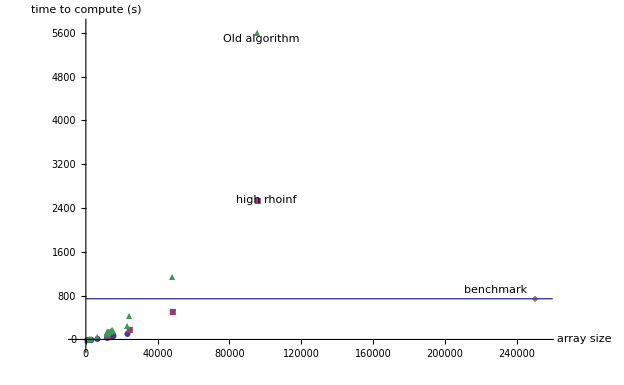

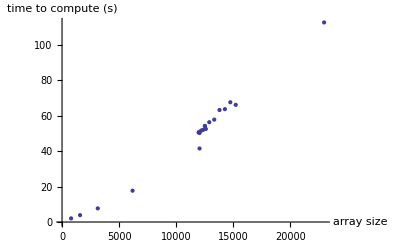

```mathematica
ListPlot[times,AxesLabel->{"array size","time to compute (s)"}](*smaller values only*)
```

### Data. Benchmark value (derived using old code): 12.6913

#### For ρinf:

```mathematica
rhoinfvals={{25000,12.324426293373108},{50000,12.319688439369202},{100000,12.317312359809875},{200000,12.316122889518738}}
```

{{25000,12.3244},{50000,12.3197},{100000,12.3173},{200000,12.3161}}

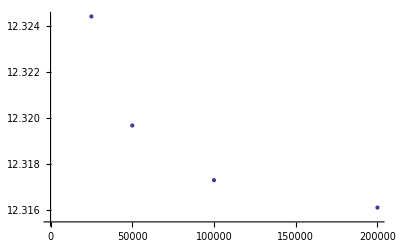

```mathematica
ListPlot[rhoinfvals]
```

This still looks asymtotic, although there are only four points shown. The total movement is not that much -- from 12.324 down to 12.316.

#### For Δρ1

```mathematica
drhovals={{0.1,12.324426293373108},{0.05,12.277984738349915},{0.025,12.252294898033142},{0.0125,12.23869001865387}}
```

{{0.1,12.3244},{0.05,12.278},{0.025,12.2523},{0.0125,12.2387}}

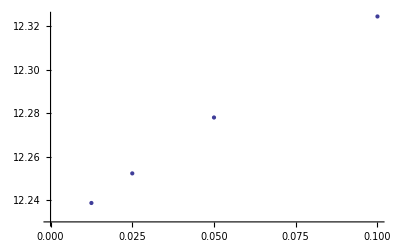

```mathematica
ListPlot[drhovals]
```

At least right here, this looks linear and very significant -- from 12.32 down to 12.24.

```mathematica
drho2vals={{8,12.488980174064636},{4,12.337796568870544},{2,12.324426293373108},{1,12.36712920665741}}
```

{{8,12.489},{4,12.3378},{2,12.3244},{1,12.3671}}

#### For Δρ2

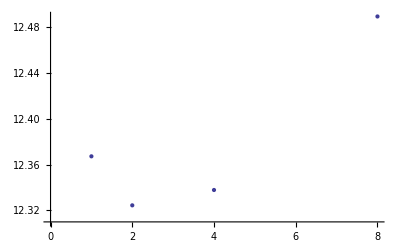

```mathematica
ListPlot[drho2vals]
```

Um...weird. It *increased* at Δρ2 = 1? I wonder if it does that even lower? At a certain point, though, Δρ2 = Δρ1 and we should recover the previous case. Here, at Δρ2 > 8, the bisection started failing, too.

```mathematica
r0vals={{50,12.47411859035492},{100,12.324426293373108},{150,12.333002924919128},{200,12.449331402778625},{250,12.583317399024963},{300,12.669992804527283},{350,12.710203051567078},{400,12.725611805915833},{450,12.730566382408142},{500,12.73152768611908}}
```

{{50,12.4741},{100,12.3244},{150,12.333},{200,12.4493},{250,12.5833},{300,12.67},{350,12.7102},{400,12.7256},{450,12.7306},{500,12.7315}}

#### For ρ0

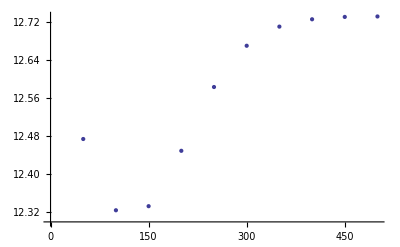

```mathematica
ListPlot[r0vals]
```

That is just really weird. This one also wasn’t done with doubling the way the others were, but uh...yeah.